```mathematica
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\StrategySpaces.wl"]
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\QPD_dynamics.wl"]
```

```mathematica
J[a,b,γ]//FullSimplify//MatrixForm
```

(1/4 (1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 ⅈ (-1+ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 ⅈ (-1-ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (-1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)-ⅇ^(ⅈ (a+b) γ))
-1/4 ⅈ (-1+ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (1-ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 ⅈ (-1-ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ))
-1/4 ⅈ (-1-ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (1-ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 ⅈ (-1+ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ))
1/4 (-1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)-ⅇ^(ⅈ (a+b) γ)) | -1/4 ⅈ (-1-ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | -1/4 ⅈ (-1+ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)))

```mathematica
Entanglement[ψ_List]:=Module[{ρFull,ρPartial,eigenvals},(*This assumes ψ is normalized*)
ρFull = Outer[Times,ψ,Conjugate[ψ]]//ComplexExpand;
ρPartial = ρFull[[{1,2},{1,2}]]+ρFull[[{3,4},{3,4}]];
eigenvals=DeleteCases[Eigenvalues[ρPartial],0];
-Total[Table[λ Log[2,λ],{λ,eigenvals}]]
]
```

```mathematica
EntangledState = (JtrigForm[a,b,γ]/ⅇ^(-1/2 ⅈ a b γ)).{1,0,0,0}//ExpToTrig//FullSimplify;
```

```mathematica
entanglement = Entanglement[EntangledState]//FullSimplify
```

(-((1+Cos[γ]) Log[Cos[γ/2]^2])+(-1+Cos[γ]) Log[Sin[γ/2]^2])/Log[4]

```mathematica
Reduce[(-((1+Cos[γ]) Log[Cos[γ/2]^2])+(-1+Cos[γ]) Log[Sin[γ/2]^2])/Log[4]==en,{γ,0,Pi/2}]
```

Reduce::ivar: 0 is not a valid variable.

Reduce[(-((1+Cos[γ]) Log[Cos[γ/2]^2])+(-1+Cos[γ]) Log[Sin[γ/2]^2])/Log[4]==en,{γ,0,π/2}]

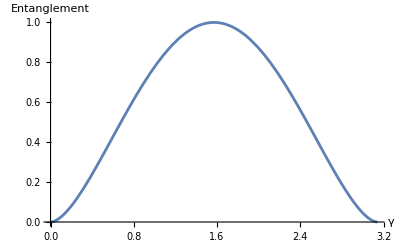

```mathematica
Plot[entanglement,{γ,0,Pi},AxesLabel->{"γ","Entanglement"}]
```

```mathematica
Maximize[entanglement,γ]
```

Maximize::ztest1: Unable to decide whether numeric quantity 2 Log[Cos[2 ArcTan[1+Times[«2»]]]]+2 Cos[4 ArcTan[1-Power[«2»]]] Log[Cos[2 ArcTan[1+Times[«2»]]]]+Cos[4 ArcTan[1-Power[«2»]]] Log[Csc[2 ArcTan[Plus[«2»]]]^2]+2 Log[Csc[«1»]]+Log[«1»]+Cos[4 ArcTan[1+√2]] Log[Sec[2 ArcTan[«1»]]^2]+Log[Sin[2 ArcTan[1+Times[«2»]]]^2]+2 Cos[4 ArcTan[1+√2]] Log[Sin[2 ArcTan[1+Power[«2»]]]] is equal to zero. Assuming it is.

{1/Log[4](-2 Log[Cos[2 ArcTan[1-√2]]]-2 Cos[4 ArcTan[1-√2]] Log[Cos[2 ArcTan[1-√2]]]-Log[Sin[2 ArcTan[1-√2]]^2]+Cos[4 ArcTan[1-√2]] Log[Sin[2 ArcTan[1-√2]]^2]),{γ→-4 ArcTan[1-√2]}}

```mathematica
JtrigForm[a,b,γ]/ⅇ^(-1/2 ⅈ a b γ)//FullSimplify//MatrixForm
```

(Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]+ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2] | -Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2] | ⅈ Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2] | ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]
Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]-ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2] | Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]+ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2] | -ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]-Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2] | ⅈ Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2]
-ⅈ Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]+Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2] | -ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]-Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2] | Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]+ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2] | -Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2]
ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2] | -ⅈ Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]+Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2] | Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]-ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2] | Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]+ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])

```mathematica
Reduce[(-((1+Cos[γ]) Log[Cos[γ/2]^2])+(-1+Cos[γ]) Log[Sin[γ/2]^2])/Log[4]==Γ&&0<γ<=Pi/2,γ]
```

$Aborted

```mathematica
-((1+Cos[γ]) Log[Cos[γ/2]^2])+(-1+Cos[γ]) Log[Sin[γ/2]^2]==Γ
```

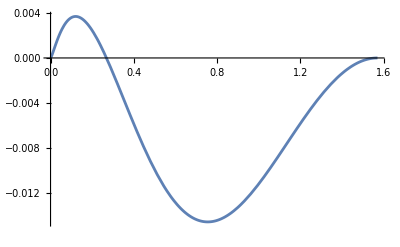

```mathematica
Plot[{(-Cos[2γ]/2+1/2)^(.77)-(-((1+Cos[γ]) Log[Cos[γ/2]^2])+(-1+Cos[γ]) Log[Sin[γ/2]^2])/Log[4]},{γ,0,Pi/2}]
```

```mathematica
FullSimplify[(-((1+Cos[γ]) Log[Cos[γ/2]^2])+(-1+Cos[γ]) Log[Sin[γ/2]^2])/Log[4]//TrigToExp//ComplexExpand,0<γ<Pi/2]
```

(Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]])/Log[4]

```mathematica
FindInstance[(Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]])/Log[4]==Γ&&0<γ<Pi/2,γ,Reals]
```

FindInstance::exvar: The system contains a nonconstant expression Γ independent of variables {γ}.

FindInstance[(Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]])/Log[4]==Γ&&0<γ<π/2,γ,ℝ]

```mathematica
(Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]])/Log[4]//TrigToExp//Simplify
```

((ⅇ^(-ⅈ γ)+ⅇ^(ⅈ γ)) Log[-(ⅈ (-1+ⅇ^(ⅈ γ)))/(1+ⅇ^(ⅈ γ))]+Log[-(16 ⅇ^(2 ⅈ γ))/((-1+ⅇ^(2 ⅈ γ))^2)])/Log[4]

```mathematica
J[a,b,γ]//FullSimplify//MatrixForm
```

(1/4 (1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 ⅈ (-1+ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 ⅈ (-1-ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (-1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)-ⅇ^(ⅈ (a+b) γ))
-1/4 ⅈ (-1+ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (1-ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 ⅈ (-1-ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ))
-1/4 ⅈ (-1-ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (1-ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 ⅈ (-1+ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ))
1/4 (-1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)-ⅇ^(ⅈ (a+b) γ)) | -1/4 ⅈ (-1-ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | -1/4 ⅈ (-1+ⅇ^(ⅈ (1+a) γ)-ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)) | 1/4 (1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)+ⅇ^(ⅈ (a+b) γ)))

```mathematica
FullSimplify[Exp[((ⅇ^(-ⅈ γ)+ⅇ^(ⅈ γ)) Log[-(ⅈ (-1+ⅇ^(ⅈ γ)))/(1+ⅇ^(ⅈ γ))]+Log[-(16 ⅇ^(2 ⅈ γ))/((-1+ⅇ^(2 ⅈ γ))^2)])/Log[4]],0<γ<Pi/2]
```

Cosh[(Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]])/Log[4]]+Sinh[(Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]])/Log[4]]

```mathematica
Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]]=G Log[4]
```

```mathematica
Exp[Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]]]==Exp[G Log[4]]
```

```mathematica
Solve[4 Csc[γ]^2 Tan[γ/2]^(2 Cos[γ])==4^G,γ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

```mathematica
4 Csc[γ]^2 Tan[γ/2]^(2 Cos[γ])//FullSimplify(*==4^(G/2)*)
```

4 Csc[γ]^2 Tan[γ/2]^(2 Cos[γ])

FittedModel[…]

0.74688

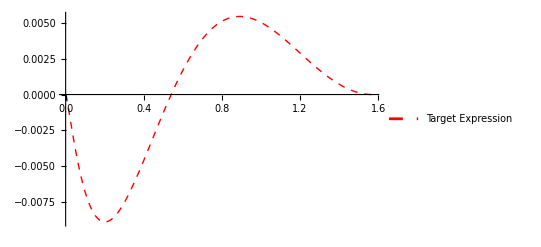

```mathematica
(*Define the target expression*)targetExpr[γ_]:=(Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]])/Log[4]

(*Generate data points for γ in a stable range (e.g.,0.1 to π-0.1)*)
data=Table[{γ,targetExpr[γ]},{γ,0.1,Pi/2-0.1,0.05}];

(*Perform the nonlinear fit for parameter p*)
fit=NonlinearModelFit[data,(-Cos[2 γ]/2+1/2)^p,{p},γ]

(*Extract the best fit value for p*)
bestP=p/. fit["BestFitParameters"]

(*Visualize the result*)
Plot[{targetExpr[γ]-fit[γ]},{γ,0,Pi/2},PlotStyle->{Thick,{Dashed,Red}},PlotLegends->{"Target Expression","Fit: sin(γ)^(2p)"}]
```

```mathematica
(Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]])/Log[4]
```

```mathematica
Sin[γ/2]^2/.γ->Pi/2
```

1/2